# Smooth code for ORT

```mathematica
Clear["Global`*"]
```

```mathematica
param={v01->1.5,v02->2,v11->2,v12->2.5,v21->1.8,v22->2.2,eta11->0,eta12->0,eta21->0,eta22->0,eta31->0,eta32->0,alfa->4,dz->2}
```

{v01→1.5,v02→2,v11→2,v12→2.5,v21→1.8,v22→2.2,eta11→0,eta12→0,eta21→0,eta22→0,eta31→0,eta32→0,alfa→4,dz→2}

```mathematica
z0=3
```

3

## V0 smoothing

## unsmoothed model

```mathematica
a=v01/.param;
```

```mathematica
b=v02/.param;
```

```mathematica
K=Piecewise[{{a,x<z0},{b,x≥z0}}]
```

Piecewise[{{1.5, x<3}, {2, x≥3}, {0, True}}]

```mathematica
m1:=a/;x<z0;
```

```mathematica
m1:=b/;x≥z0;
```

```mathematica
FF=K*E^(2*(x-z0)^2)/.param;
```

```mathematica
F1=(Integrate[FF,{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

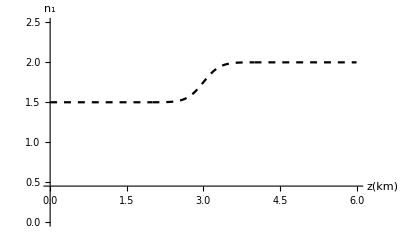

```mathematica
å1=Plot[F1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0.45},PlotRange->{{0,6},{0,2.5}},AxesLabel->{Style["z(km)",FontSize->15],Style["n_1",FontSize->15]}]
```

```mathematica
(*HeavisideTheta*)
```

## V1 smoothing

## smoothed model

```mathematica
a1=v11/.param;
```

```mathematica
b1=v12/.param;
```

```mathematica
K1=Piecewise[{{a1,x<z0},{b1,x≥z0}}]
```

Piecewise[{{2, x<3}, {2.5, x≥3}, {0, True}}]

## unsmooth model for V1

```mathematica
m2:=a1/;x<z0;
```

```mathematica
m2:=b1/;x≥z0;
```

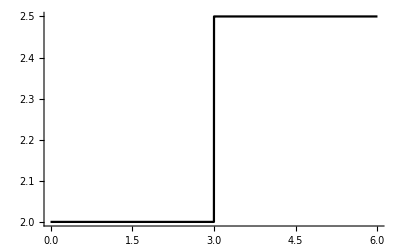

```mathematica
L11=Plot[m2,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Fn1=(Integrate[K1*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

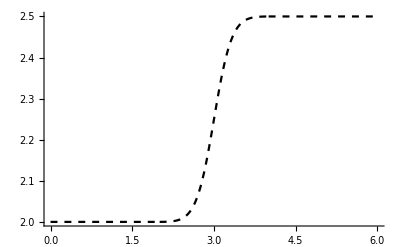

```mathematica
L12=Plot[Fn1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

## V2 smoothing

## smoothed model

```mathematica
a2=v21/.param;
```

```mathematica
b2=v22/.param;
```

```mathematica
K2=Piecewise[{{a2,x<z0},{b2,x≥z0}}]
```

Piecewise[{{1.8, x<3}, {2.2, x≥3}, {0, True}}]

## unsmooth model for V2

```mathematica
m3:=a2/;x<z0;
```

```mathematica
m3:=b2/;x≥z0;
```

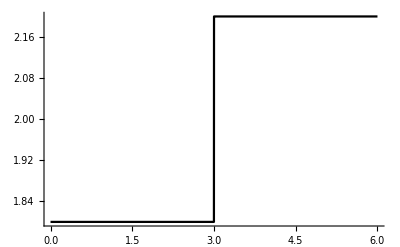

```mathematica
L21=Plot[m3,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Fn2=(Integrate[K2*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

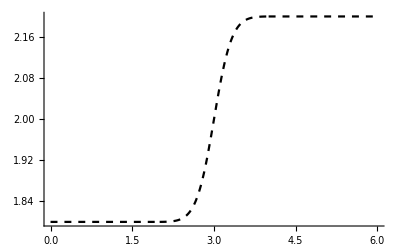

```mathematica
L22=Plot[Fn2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

## eta1 smoothing

## composite param

```mathematica
a3=eta11/.param;
```

```mathematica
b3=eta12/.param;
```

```mathematica
K3=Piecewise[{{a3,x<z0},{b3,x≥z0}}]
```

0

## unsmooth model for m3

```mathematica
m4:=a3/;x<z0;
```

```mathematica
m4:=b3/;x≥z0;
```

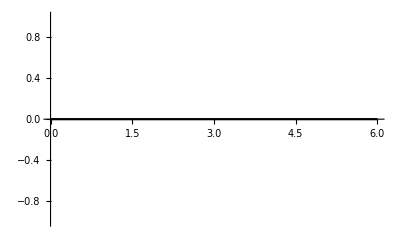

```mathematica
Le1=Plot[m4,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
Fn1e=(Integrate[K3*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

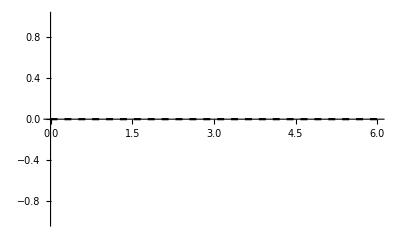

```mathematica
Le2=Plot[Fn1e,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

## eta2 smoothing

## composite param

```mathematica
a4=eta21/.param;
```

```mathematica
b4=eta22/.param;
```

```mathematica
K4=Piecewise[{{a4,x<z0},{b4,x≥z0}}]
```

0

## unsmooth model for n5

```mathematica
m5:=a4/;x<z0;
```

```mathematica
m5:=b4/;x≥z0;
```

```mathematica
Le11=Plot[m5,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Fn2e=(Integrate[K4*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

## eta3 smoothing

## composite param

```mathematica
a5=eta31/.param;
```

```mathematica
b5=eta32/.param;
```

```mathematica
K5=Piecewise[{{a5,x<z0},{b5,x≥z0}}]
```

0

## unsmooth model for n5

```mathematica
m6:=a5/;x<z0;
```

```mathematica
m6:=b5/;x≥z0;
```

```mathematica
Le31=Plot[m6,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Fn3e=(Integrate[K5*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Le32=Plot[Fn3e,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

## convert to the model parameters

```mathematica
V0=F1;
```

```mathematica
Vnmo1=Fn1;
```

```mathematica
Vnmo2=Fn2;
```

```mathematica
ETA1=Fn1e;
```

```mathematica
ETA2=Fn2e;
```

```mathematica
ETA3=Fn3e;
```

## unsmoothed model parameters v0

```mathematica
vel0:=v01/;z<z0;
```

```mathematica
vel0:=v02/;z≥z0;
```

```mathematica
p10=Plot[vel0/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p11=Plot[V0,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

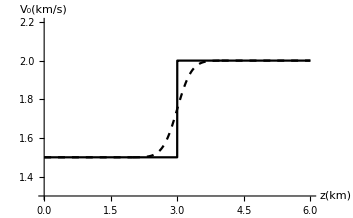

```mathematica
Show[{p10,p11},AxesOrigin->{0,1.3},PlotRange->{{0,6},{1.3,2.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_0(km/s)",FontSize->15]}]
```

## unsmoothed model parameters v1

```mathematica
vel1:=v11/;z<z0;
```

```mathematica
vel1:=v12/;z≥z0;
```

```mathematica
p20=Plot[vel1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p21=Plot[Vnmo1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

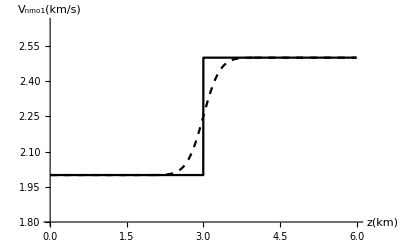

```mathematica
Show[{p20,p21},AxesOrigin->{0,1.8},PlotRange->{{0,6},{1.8,2.65}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo1(km/s)",FontSize->15]}]
```

## unsmoothed model parameters v2

```mathematica
vel2:=v21/;z<z0;
```

```mathematica
vel2:=v22/;z≥z0;
```

```mathematica
p30=Plot[vel2/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p31=Plot[Vnmo2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

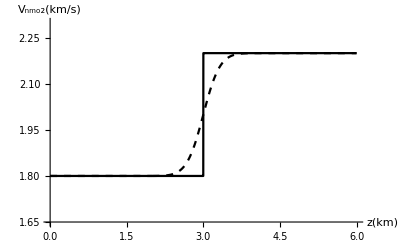

```mathematica
Show[{p30,p31},AxesOrigin->{0,1.65},PlotRange->{{0,6},{1.65,2.3}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo2(km/s)",FontSize->15]}]
```

## unsmoothed model parameters eta1

```mathematica
et1:=eta11/;z<z0;
```

```mathematica
et1:=eta12/;z≥z0;
```

```mathematica
p40=Plot[et1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p41=Plot[ETA1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

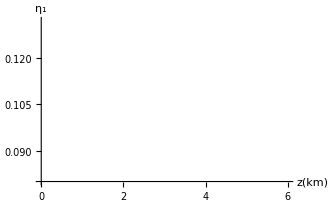

```mathematica
Show[{p40,p41},AxesOrigin->{0,0.08},PlotRange->{{0,6},{0.08,0.132}},AxesLabel->{Style["z(km)",FontSize->15],Style["η_1",FontSize->15]}]
```

## unsmoothed model parameters eta2

```mathematica
et2:=eta21/;z<z0;
```

```mathematica
et2:=eta22/;z≥z0;
```

```mathematica
p50=Plot[et2/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p51=Plot[ETA2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

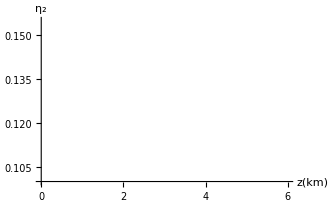

```mathematica
Show[{p50,p51},AxesOrigin->{0,0.1},PlotRange->{{0,6},{0.1,0.155}},AxesLabel->{Style["z(km)",FontSize->15],Style["η_2",FontSize->15]}]
```

## unsmoothed model parameters etaxy

```mathematica
et3:=eta31/;z<z0;
```

```mathematica
et3:=eta32/;z≥z0;
```

```mathematica
p60=Plot[et3/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
p61=Plot[ETA3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

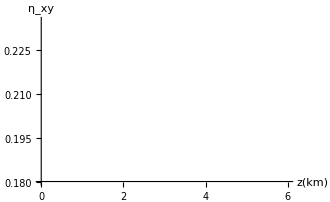

```mathematica
Show[{p60,p61},AxesOrigin->{0,0.18},PlotRange->{{0,6},{0.18,0.235}},AxesLabel->{Style["z(km)",FontSize->15],Style["η_xy",FontSize->15]}]
```

## convert into eta3

```mathematica
Et3=(((1+2*ETA1)*(1+2*ETA2)/(1+ETA3)^2)-1)/2;
```

```mathematica
p70=Plot[1/2 (-1+((1+2 et1) (1+2 et2))/(1+et3)^2)/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

```mathematica
p71=Plot[Et3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

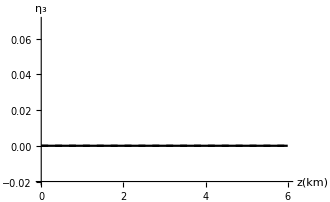

```mathematica
Show[{p70,p71},AxesOrigin->{0,-0.02},PlotRange->{{0,6},{-0.02,0.07}},AxesLabel->{Style["z(km)",FontSize->15],Style["η_3",FontSize->15]}]
```

## Traveltime Error

```mathematica
Xpp=Sum[(px vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2 *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.001}];
```

```mathematica
(*O2=(py*vel2^2*z*Th1)/(f2^(3/2)*f1^(1/2)*vel0)*)
```

```mathematica
Ypp=Sum[(py (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2 *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.001}];
```

```mathematica
(*O3=(z*(f1*f2+px^2*vel1^2*Th2+py^2*vel2^2*Th1))/(f2^(3/2)*f1^(1/2)*vel0)*)
```

```mathematica
Tpp=Sum[((py^2 (-1+(2 et1-et3) px^2 vel1^2)^2 vel2^2+px^2 vel1^2 (-1+(2 et2-et3) py^2 vel2^2)^2+(1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2) (1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2)) *0.001)/(vel0 (1-2 et1 px^2 vel1^2-2 et2 py^2 vel2^2+(4 et1 et2-et3^2) px^2 py^2 vel1^2 vel2^2)^(3/2) √(1-(1+2 et1) px^2 vel1^2-(1+2 et2) py^2 vel2^2+((1+2 et1) (1+2 et2)-(1+et3)^2) px^2 py^2 vel1^2 vel2^2))/.param,{z,0,6,0.001}];
```

```mathematica
ParametricPlot3D[{Xpp,Ypp,Tpp},{px,0,0.9},{py,0,0.9},PlotRange->{{0,6},{0,6},{3.5,5.2}},AxesLabel->{Style["x(km)",FontSize->15],Style["y(km)",FontSize->15],Style["T_exact(s)",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<7&&Abs[v]<7&&3.5<w<5.5],ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

## ETA3 here means ETAxy

#### For PTS

```mathematica
f11=1-(1+2*ETA1)*px^2*Vnmo1^2-(1+2*ETA2)*py^2*Vnmo2^2+((1+2*ETA1)*(1+2*ETA2)-(1+ETA3)^2)*px^2*py^2*Vnmo1^2*Vnmo2^2;
```

```mathematica
f22=1-2*ETA1*px^2*Vnmo1^2-2*ETA2*py^2*Vnmo2^2+(4*ETA1*ETA2-ETA3^2)*px^2*py^2*Vnmo1^2*Vnmo2^2;
```

```mathematica
Th11=((2*ETA1-ETA3)*px^2*Vnmo1^2-1)^2;
```

```mathematica
Th22=((2*ETA2-ETA3)*py^2*Vnmo2^2-1)^2;
```

```mathematica
Xppp=Sum[((px*Vnmo1^2*0.001*Th22)/(f22^(3/2)*f11^(1/2)*V0))/.param,{z,0,6,0.001}];
```

```mathematica
Yppp=Sum[(py*Vnmo2^2*0.001*Th11)/(f22^(3/2)*f11^(1/2)*V0)/.param,{z,0,6,0.001}];
```

```mathematica
Tppp=Sum[(0.001*(f11*f22+px^2*Vnmo1^2*Th22+py^2*Vnmo2^2*Th11))/(f22^(3/2)*f11^(1/2)*V0)/.param,{z,0,6,0.001}];
```

```mathematica
DT=Abs[(Tpp-Tppp)];
```

```mathematica
CRT=DT/.px->0/.py->0;
```

```mathematica
DT/.px->0/.py->0
```

0.00711357

```mathematica
ParametricPlot3D[{Xpp/6,Ypp/6,Abs[DT-CRT]},{px,0,0.9},{py,0,0.9},PlotRange->{{0,1},{0,1},{0,0.02}},AxesLabel->{Style["x/z  ",FontSize->15],Style["y/z  ",FontSize->15],Style["|ΔT|(s)       ",FontSize->15]},BoxRatios->{1, 1,0.5},RegionFunction->Function[{u,v,w},Abs[u]<9&&Abs[v]<9&&0<w<0.04],ColorFunction->(ColorData["TemperatureMap",#3*10]&)]
```

-Graphics3D-